Parameter w1

```mathematica
y={1,-1,1,-1,-1,-1,1,1,1,1,1,-1,1,-1,-1,-1,1,1,1,1};
x1 = {6,8,-1,0,5,1.2,-2,9.8,4,12,1,10,1,2.2,-6,9.8,1,1,1,1};
```

```mathematica
(*Derive alice PDF*)
pNoNorm[w1_, w2_]:=Exp[(Plus@@Table[Boole[y[[i]] * (x1[[i]] * w1 + w2) >= 0],{i,Length[y]}])] * PDF[UniformDistribution[{-8, 8}], w1] * PDF[UniformDistribution[{-8, 8}], w2]
```

```mathematica
normConstant = N[Integrate[pNoNorm[w1,w2],{w1,-8,8},{w2,-8,8}]]
```

119963.

```mathematica
p[w1_]=Integrate[pNoNorm[w1, w2]/normConstant,{w2,-8, 8}]
```

Piecewise[{{Piecewise[{{0.00288736, w1==-8.}, {3.25621×10^-8 (1.30204×10^6+59874.1 w1), w1==8.}, {3.25621×10^-8 (1.30527×10^6+59470.7 w1), 6.66667<w1<8.}, {6.51242×10^-9 (6.51019×10^6+299774. w1), w1==6.66667}, {6.51242×10^-9 (6.55406×10^6+293194. w1), 4.<w1<6.66667}, {-6.51242×10^-8 (-662943.+506150. w1), w1==0.}, {6.51242×10^-9 (43865.3+1.92074×10^6 w1), w1==4.}, {-6.51242×10^-9 (-1.76965×10^7+2.49133×10^6 w1), w1==3.63636}, {-6.51242×10^-9 (-1.77404×10^7+2.50339×10^6 w1), 3.63636<w1<4.}, {-6.51242×10^-9 (-1.76965×10^7+2.45902×10^6 w1), w1==1.6}, {-6.51242×10^-9 (-1.77404×10^7+2.48643×10^6 w1), 1.6<w1<2.}, {-6.51242×10^-9 (-1.78158×10^7+2.52412×10^6 w1), 2.≤w1<3.63636}, {-6.51242×10^-9 (-1.78158×10^7+2.53354×10^6 w1), 1.33333≤w1<1.6}, {6.51242×10^-9 (6.62943×10^6+5.83737×10^6 w1), 0.8<w1<0.816327||0.816327<w1<1.}, {6.51242×10^-9 (6.55406×10^6+5.91275×10^6 w1), 1.<w1<1.33333}, {6.51242×10^-9 (6.51019×10^6+5.95661×10^6 w1), w1==1.}, {6.51242×10^-9 (6.51019×10^6+5.98344×10^6 w1), w1==0.816327}, {6.51242×10^-9 (6.51019×10^6+5.98642×10^6 w1), w1==0.8}, {6.51242×10^-9 (6.83432×10^6+5.58127×10^6 w1), 0.666667≤w1<0.8}, {6.51242×10^-9 (6.62943×10^6+5.8886×10^6 w1), 0.<w1<0.666667}, {3.25621×10^-8 (9.64468×10^6+1.1945×10^6 w1), -8.<w1≤-6.66667}, {-6.51242×10^-9 (-1.78158×10^7-5.36427×10^6 w1), -1.33333<w1≤-1.}, {-6.51242×10^-9 (-1.77404×10^7-3.90944×10^6 w1), -2.<w1≤-1.6}, {-6.51242×10^-9 (-1.78158×10^7-1.41136×10^6 w1), -6.66667<w1≤-4.}, {-6.51242×10^-9 (-1.77404×10^7-1.39252×10^6 w1), -4.<w1≤-3.63636}, {-6.51242×10^-9 (-6.55406×10^6+1.68373×10^6 w1), -3.63636<w1≤-2.}, {-6.51242×10^-9 (-6.55406×10^6+3.08202×10^6 w1), -1.6<w1≤-1.33333}, {-6.51242×10^-9 (-6.62943×10^6+4.79327×10^6 w1), -0.666667<w1<0.}, {-6.51242×10^-9 (-6.62943×10^6+5.82208×10^6 w1), -1.<w1≤-0.8}, {-6.51242×10^-9 (-2.5142×10^6+1.09661×10^7 w1), True}}], -8.≤w1≤8.}, {0., True}}]

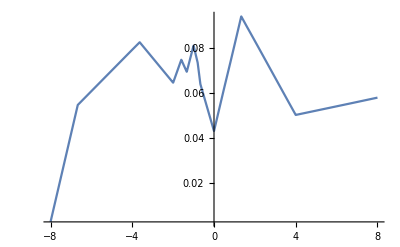

```mathematica
(*Visulize PDF*)
Plot[p[w1],{w1,-8,8},PlotRange->Full]
```

```mathematica
cdf[w1_]:=Integrate[p[t],{t,-Infinity,w1}]
```

```mathematica
Range[-8, 8, 0.16]
```

{-8.,-7.84,-7.68,-7.52,-7.36,-7.2,-7.04,-6.88,-6.72,-6.56,-6.4,-6.24,-6.08,-5.92,-5.76,-5.6,-5.44,-5.28,-5.12,-4.96,-4.8,-4.64,-4.48,-4.32,-4.16,-4.,-3.84,-3.68,-3.52,-3.36,-3.2,-3.04,-2.88,-2.72,-2.56,-2.4,-2.24,-2.08,-1.92,-1.76,-1.6,-1.44,-1.28,-1.12,-0.96,-0.8,-0.64,-0.48,-0.32,-0.16,0.,0.16,0.32,0.48,0.64,0.8,0.96,1.12,1.28,1.44,1.6,1.76,1.92,2.08,2.24,2.4,2.56,2.72,2.88,3.04,3.2,3.36,3.52,3.68,3.84,4.,4.16,4.32,4.48,4.64,4.8,4.96,5.12,5.28,5.44,5.6,5.76,5.92,6.08,6.24,6.4,6.56,6.72,6.88,7.04,7.2,7.36,7.52,7.68,7.84,8.}

```mathematica
cdf /@ Range[-8, 8, 0.16]
```

{0.,0.000959838,0.0029154,0.00586668,0.00981369,0.0147564,0.0206949,0.0276291,0.035559,0.0443156,0.0533498,0.0626193,0.0721241,0.0818641,0.0918395,0.10205,0.112496,0.123177,0.134094,0.145246,0.156633,0.168256,0.180113,0.192206,0.204535,0.217098,0.229896,0.242925,0.256051,0.268916,0.2815,0.293803,0.305825,0.317567,0.329028,0.340208,0.351107,0.361726,0.372181,0.383171,0.394812,0.406523,0.417798,0.429654,0.442347,0.454593,0.465454,0.475159,0.484064,0.492171,0.499478,0.506877,0.515257,0.524619,0.534963,0.546271,0.558531,0.571768,0.585991,0.600886,0.615437,0.62957,0.643288,0.656591,0.669474,0.681936,0.693977,0.705597,0.716797,0.727575,0.737933,0.74787,0.757386,0.766482,0.775159,0.783419,0.791495,0.79962,0.807793,0.816015,0.824287,0.832607,0.840976,0.849394,0.85786,0.866376,0.87494,0.883554,0.892216,0.900927,0.909687,0.918496,0.927354,0.936261,0.945218,0.954224,0.96328,0.972386,0.981541,0.990746,1.}

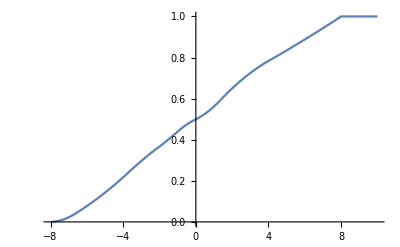

```mathematica
(*Visulize CDF*)
Plot[cdf[w1],{w1,-8,10}]
```

```mathematica
[cdf[t], {t, -8, 8}]
```

Syntax::tsntxi: "[cdf[t],{t,-8,8}]" is incomplete; more input is needed.

```mathematica
a := ProbabilityDistribution[p[w1], {w1, -8, 8}]
Mean[a]
Variance[a]
```

0.0565823

18.2305

Parameter w2

```mathematica
p[w2_]=Integrate[pNoNorm[w1, w2]/normConstant,{w1,-8, 8}]
```

Piecewise[{{Piecewise[{{-2.46682×10^-11 (-3.57391×10^7+948700. w2), w2==-8.}, {3.25621×10^-8 (1.36686×10^6+170858. w2), w2==0.}, {2.46682×10^-11 (1.80426×10^9+2.20116×10^8 w2), -8.<w2<0.}, {2.46682×10^-11 (6.6375×10^8+8.69925×10^8 w2), 0.<w2<8.}, {-2.46682×10^-11 (-1.44182×10^10+8.4938×10^8 w2), True}}], -8.≤w2≤8.}, {0., True}}]

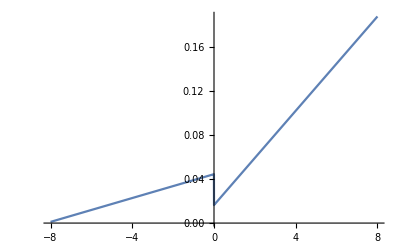

```mathematica
(*Visulize PDF*)
Plot[p[w2],{w2,-8,8},PlotRange->Full]
```

```mathematica
cdf[w2_]:=NIntegrate[p[t],{t,-8,w2}]
```

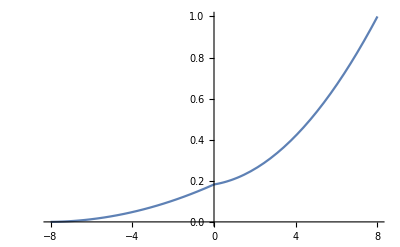

```mathematica
(*Visulize CDF*)
Plot[cdf[w2],{w2,-8,8}]
```

```mathematica
a := ProbabilityDistribution[p[w2], {w2, -8, 8}]
Mean[a]
Variance[a]
```

3.68883

13.1973

```mathematica
cdf[x1_]=Integrate[p[t],{t,-Infinity,x1}]
```